```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
matrix1 = Import["matrix_conv1.txt","Table"]
```

{{6,6,8,5,5},{6,8,5,5,5},{8,5,5,5,5},{5,5,5,5,6},{5,5,5,6,6}}

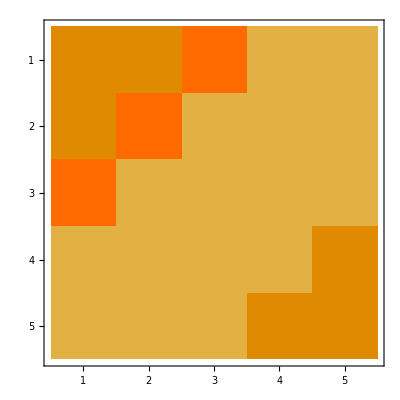

```mathematica
MatrixPlot[matrix1]
```

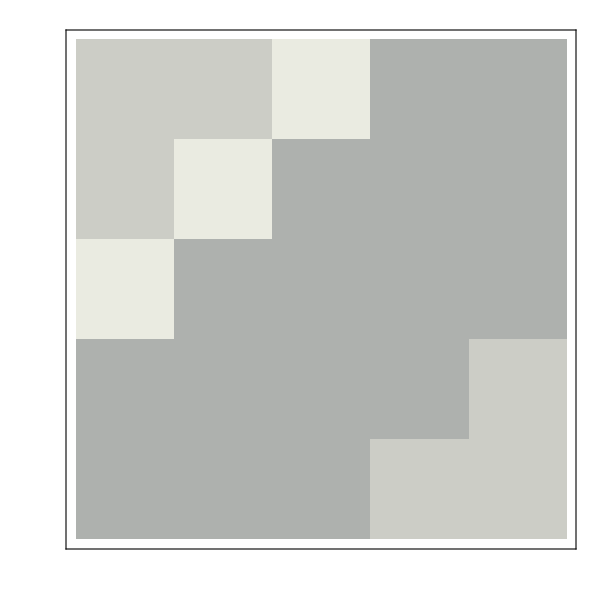

```mathematica
MatrixPlot[matrix1,ColorFunction->"GrayTones",FrameTicks->{Table[{i,+10-20/300*i},{i,0,300,30}],Table[{i,-10+20/300*i},{i,0,300,30}]},Epilog->{{Red,PointSize[Large],Point[{(4+10)/(2/30),(-1+10)/(2/30)}]},{Red,PointSize[Large],Point[{(-4+10)/(2/30),(1+10)/(2/30)}]}},ImageSize->600]
```

```mathematica
matrix2 = Import["matrix_con2.txt","Table"];
```

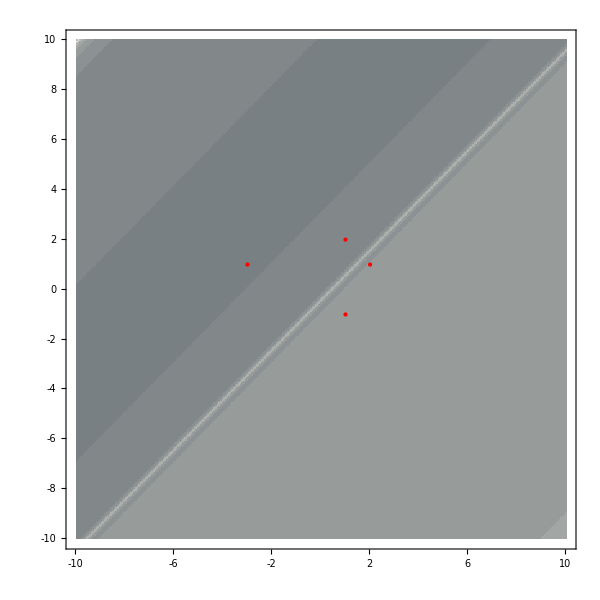

```mathematica
MatrixPlot[matrix2,ColorFunction->"GrayTones",FrameTicks->{Table[{i,+10-20/300*i},{i,0,300,30}],Table[{i,-10+20/300*i},{i,0,300,30}]},Epilog->{{Red,PointSize[Large],Point[{(-3+10)/(2/30),(1+10)/(2/30)}]},{Red,PointSize[Large],Point[{(1+10)/(2/30),(-1+10)/(2/30)}]},{Red,PointSize[Large],Point[{(1+10)/(2/30),(2+10)/(2/30)}]},{Red,PointSize[Large],Point[{(2+10)/(2/30),(1+10)/(2/30)}]}},ImageSize->600]
```

```mathematica
Graphics
```

```mathematica
matrix3 = Import["matrix_conv3.txt","Table"];
```

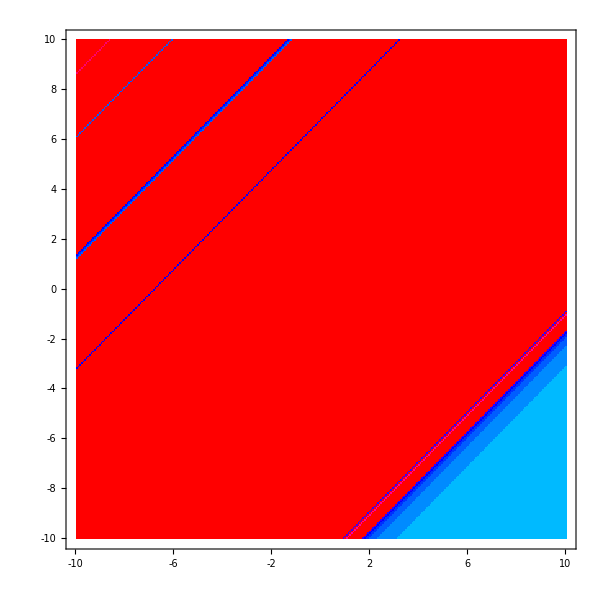

```mathematica
MatrixPlot[matrix3,ColorFunction->Hue,FrameTicks->{Table[{i,+10-20/300*i},{i,0,300,30}],Table[{i,-10+20/300*i},{i,0,300,30}]},Epilog->{{Red,PointSize[Large],Point[{(-3+10)/(2/30),(1+10)/(2/30)}]},{Red,PointSize[Large],Point[{(1+10)/(2/30),(-1+10)/(2/30)}]},{Red,PointSize[Large],Point[{(1+10)/(2/30),(2+10)/(2/30)}]},{Red,PointSize[Large],Point[{(2+10)/(2/30),(1+10)/(2/30)}]}},ImageSize->600]
```

```mathematica
NSolve[{2*(x+y)*(x+y)+(x-y)*(x-y)-8==0,5*x*x+(y-3)*(y-3)-9},{x,y}]
```

{{x→-0.566803-1.9495 ⅈ,y→-2.24464+1.05344 ⅈ},{x→-0.566803+1.9495 ⅈ,y→-2.24464-1.05344 ⅈ},{x→1.,y→1.},{x→-1.18347,y→1.58684}}